```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};
Wxmin= {2,3,1};
Wxmax= {5,3,1};
Hymin= {3,2,1};
Hymax= {3,5,1};
WorldPoints = {a,b,c,d,aPrime,bPrime,cPrime,dPrime,d2Prime};
Oc={0,0,0,1};
zeta1 = -1;
zeta2=-1;
alpha=10;
beta = -10;
Oc2={6,0,0,1};
Rot2=RotationsE2[alpha];
Rot1=RotationsE2[beta];
ObjectSize = b[[1]]-a[[1]];
A={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
AK={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
ClearAll["Global`*"];
```

PM1 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

OC2 = {6,0,0,1}

M of C2=(Cos[10 °] | 0 | Sin[10 °] | 0
0 | 1 | 0 | 0
-Sin[10 °] | 0 | Cos[10 °] | 0
0 | 0 | 0 | 1)

M2 of C1 =(0.984808 | 0. | -0.173648 | -5.90885
0. | 1. | 0. | 0.
0.173648 | 0. | 0.984808 | -1.04189
0. | 0. | 0. | 1.)

ProjectionMtxCamera1(-Cos[10 °] | 0 | -Sin[10 °] | 0
0 | -1 | 0 | 0
Sin[10 °] | 0 | -Cos[10 °] | 0
-Sin[10 °] | 0 | Cos[10 °] | 0)

ProjectionMtxCamera2(-0.984808 | 0. | 0.173648 | 5.90885
0. | -1. | 0. | 0.
-0.173648 | 0. | -0.984808 | 1.04189
0.173648 | 0. | 0.984808 | -1.04189)

CameraProjectedPointsK1 = (-3 Cos[10 °]+4 Sin[10 °] | -3 | 4 Cos[10 °]+3 Sin[10 °] | -4 Cos[10 °]-3 Sin[10 °]
-5 Cos[10 °]+4 Sin[10 °] | -3 | 4 Cos[10 °]+5 Sin[10 °] | -4 Cos[10 °]-5 Sin[10 °]
-5 Cos[10 °]+4 Sin[10 °] | -5 | 4 Cos[10 °]+5 Sin[10 °] | -4 Cos[10 °]-5 Sin[10 °]
-3 Cos[10 °]+4 Sin[10 °] | -5 | 4 Cos[10 °]+3 Sin[10 °] | -4 Cos[10 °]-3 Sin[10 °]
-3 Cos[10 °]+6 Sin[10 °] | -3 | 6 Cos[10 °]+3 Sin[10 °] | -6 Cos[10 °]-3 Sin[10 °]
-5 Cos[10 °]+6 Sin[10 °] | -3 | 6 Cos[10 °]+5 Sin[10 °] | -6 Cos[10 °]-5 Sin[10 °]
-5 Cos[10 °]+6 Sin[10 °] | -5 | 6 Cos[10 °]+5 Sin[10 °] | -6 Cos[10 °]-5 Sin[10 °]
-3 Cos[10 °]+6 Sin[10 °] | -5 | 6 Cos[10 °]+3 Sin[10 °] | -6 Cos[10 °]-3 Sin[10 °]
-8 Cos[10 °]+6 Sin[10 °] | -8 | 6 Cos[10 °]+8 Sin[10 °] | -6 Cos[10 °]-8 Sin[10 °])

CameraProjectedPointsK2 = (2.25983 | -3. | 4.46018 | -4.46018
0.290215 | -3. | 4.11288 | -4.11288
0.290215 | -5. | 4.11288 | -4.11288
2.25983 | -5. | 4.46018 | -4.46018
1.91253 | -3. | 6.42979 | -6.42979
-0.0570813 | -3. | 6.08249 | -6.08249
-0.0570813 | -5. | 6.08249 | -6.08249
1.91253 | -5. | 6.42979 | -6.42979
-3.0115 | -8. | 5.56155 | -5.56155)

homogene CameraProjectedPointsK1 = ((-3 Cos[10 °]+4 Sin[10 °])/(-4 Cos[10 °]-3 Sin[10 °]) | -3/(-4 Cos[10 °]-3 Sin[10 °]) | (4 Cos[10 °]+3 Sin[10 °])/(-4 Cos[10 °]-3 Sin[10 °]) | 1
(-5 Cos[10 °]+4 Sin[10 °])/(-4 Cos[10 °]-5 Sin[10 °]) | -3/(-4 Cos[10 °]-5 Sin[10 °]) | (4 Cos[10 °]+5 Sin[10 °])/(-4 Cos[10 °]-5 Sin[10 °]) | 1
(-5 Cos[10 °]+4 Sin[10 °])/(-4 Cos[10 °]-5 Sin[10 °]) | -5/(-4 Cos[10 °]-5 Sin[10 °]) | (4 Cos[10 °]+5 Sin[10 °])/(-4 Cos[10 °]-5 Sin[10 °]) | 1
(-3 Cos[10 °]+4 Sin[10 °])/(-4 Cos[10 °]-3 Sin[10 °]) | -5/(-4 Cos[10 °]-3 Sin[10 °]) | (4 Cos[10 °]+3 Sin[10 °])/(-4 Cos[10 °]-3 Sin[10 °]) | 1
(-3 Cos[10 °]+6 Sin[10 °])/(-6 Cos[10 °]-3 Sin[10 °]) | -3/(-6 Cos[10 °]-3 Sin[10 °]) | (6 Cos[10 °]+3 Sin[10 °])/(-6 Cos[10 °]-3 Sin[10 °]) | 1
(-5 Cos[10 °]+6 Sin[10 °])/(-6 Cos[10 °]-5 Sin[10 °]) | -3/(-6 Cos[10 °]-5 Sin[10 °]) | (6 Cos[10 °]+5 Sin[10 °])/(-6 Cos[10 °]-5 Sin[10 °]) | 1
(-5 Cos[10 °]+6 Sin[10 °])/(-6 Cos[10 °]-5 Sin[10 °]) | -5/(-6 Cos[10 °]-5 Sin[10 °]) | (6 Cos[10 °]+5 Sin[10 °])/(-6 Cos[10 °]-5 Sin[10 °]) | 1
(-3 Cos[10 °]+6 Sin[10 °])/(-6 Cos[10 °]-3 Sin[10 °]) | -5/(-6 Cos[10 °]-3 Sin[10 °]) | (6 Cos[10 °]+3 Sin[10 °])/(-6 Cos[10 °]-3 Sin[10 °]) | 1
(-8 Cos[10 °]+6 Sin[10 °])/(-6 Cos[10 °]-8 Sin[10 °]) | -8/(-6 Cos[10 °]-8 Sin[10 °]) | (6 Cos[10 °]+8 Sin[10 °])/(-6 Cos[10 °]-8 Sin[10 °]) | 1)

homogene CameraProjectedPointsK2 = (-0.506669 | 0.672619 | -1. | 1.
-0.0705625 | 0.729416 | -1. | 1.
-0.0705625 | 1.21569 | -1. | 1.
-0.506669 | 1.12103 | -1. | 1.
-0.297449 | 0.466578 | -1. | 1.
0.00938452 | 0.493219 | -1. | 1.
0.00938452 | 0.822031 | -1. | 1.
-0.297449 | 0.77763 | -1. | 1.
0.541487 | 1.43845 | -1. | 1.)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

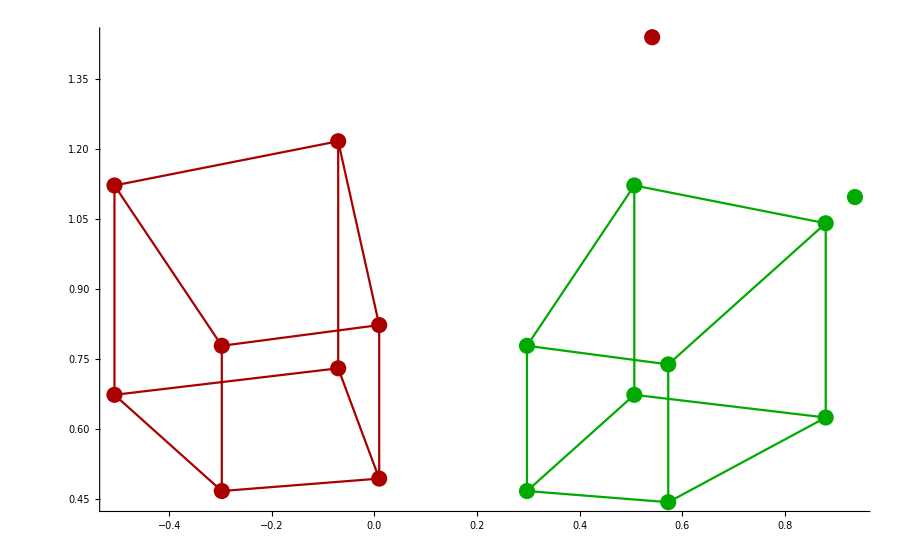

ImagePlaneC1Points = ((3 Cos[10 °]-4 Sin[10 °])/(4 Cos[10 °]+3 Sin[10 °]) | 3/(4 Cos[10 °]+3 Sin[10 °]) | 1
(5 Cos[10 °]-4 Sin[10 °])/(4 Cos[10 °]+5 Sin[10 °]) | 3/(4 Cos[10 °]+5 Sin[10 °]) | 1
(5 Cos[10 °]-4 Sin[10 °])/(4 Cos[10 °]+5 Sin[10 °]) | 5/(4 Cos[10 °]+5 Sin[10 °]) | 1
(3 Cos[10 °]-4 Sin[10 °])/(4 Cos[10 °]+3 Sin[10 °]) | 5/(4 Cos[10 °]+3 Sin[10 °]) | 1
(Cos[10 °]-2 Sin[10 °])/(2 Cos[10 °]+Sin[10 °]) | 1/(2 Cos[10 °]+Sin[10 °]) | 1
(5 Cos[10 °]-6 Sin[10 °])/(6 Cos[10 °]+5 Sin[10 °]) | 3/(6 Cos[10 °]+5 Sin[10 °]) | 1
(5 Cos[10 °]-6 Sin[10 °])/(6 Cos[10 °]+5 Sin[10 °]) | 5/(6 Cos[10 °]+5 Sin[10 °]) | 1
(Cos[10 °]-2 Sin[10 °])/(2 Cos[10 °]+Sin[10 °]) | 5/(3 (2 Cos[10 °]+Sin[10 °])) | 1
(4 Cos[10 °]-3 Sin[10 °])/(3 Cos[10 °]+4 Sin[10 °]) | 4/(3 Cos[10 °]+4 Sin[10 °]) | 1)

ImagePlaneC2Points = (-0.506669 | 0.672619 | 1.
-0.0705625 | 0.729416 | 1.
-0.0705625 | 1.21569 | 1.
-0.506669 | 1.12103 | 1.
-0.297449 | 0.466578 | 1.
0.00938452 | 0.493219 | 1.
0.00938452 | 0.822031 | 1.
-0.297449 | 0.77763 | 1.
0.541487 | 1.43845 | 1.)

CoefficientMtx = (-0.256713 | -0.340795 | -0.506669 | 0.340795 | 0.452417 | 0.672619 | 0.506669 | 0.672619 | 1.
-0.0620784 | -0.044033 | -0.0705625 | 0.641715 | 0.455176 | 0.729416 | 0.879765 | 0.624029 | 1.
-0.0620784 | -0.0733884 | -0.0705625 | 1.06952 | 1.26438 | 1.21569 | 0.879765 | 1.04005 | 1.
-0.256713 | -0.567992 | -0.506669 | 0.567992 | 1.25671 | 1.12103 | 0.506669 | 1.12103 | 1.
-0.0884758 | -0.138783 | -0.297449 | 0.138783 | 0.217695 | 0.466578 | 0.297449 | 0.466578 | 1.
0.00537578 | 0.00415423 | 0.00938452 | 0.282533 | 0.218332 | 0.493219 | 0.572835 | 0.442668 | 1.
0.00537578 | 0.00692371 | 0.00938452 | 0.470888 | 0.606478 | 0.822031 | 0.572835 | 0.73778 | 1.
-0.0884758 | -0.231305 | -0.297449 | 0.231305 | 0.604709 | 0.77763 | 0.297449 | 0.77763 | 1.
0.507248 | 0.59357 | 0.541487 | 1.34749 | 1.57681 | 1.43845 | 0.936769 | 1.09619 | 1.)

MatrixRank[CoefficientMtx]8

ns ={{-1.53203×10^-15,-0.122788,5.68777×10^-16,-0.122788,2.25388×10^-16,0.696364,-4.0662×10^-16,-0.696364,2.4795×10^-16}}

F = (-1.53203×10^-15 | -0.122788 | 5.68777×10^-16
-0.122788 | 2.25388×10^-16 | 0.696364
-4.0662×10^-16 | -0.696364 | 2.4795×10^-16)

lC1 = {{-0.0825894,0.634152,-0.468388},{-0.0766231,0.58834,-0.434551},{-0.127705,0.58834,-0.724252},{-0.137649,0.634152,-0.780647},{-0.0572901,0.659841,-0.324908},{-0.0543542,0.626027,-0.308258},{-0.0905904,0.626027,-0.513764},{-0.0954835,0.659841,-0.541514},{-0.134598,0.58134,-0.763345}}

lPrimeC1 = {{-0.0825894,-0.634152,0.468388},{-0.0895634,-0.6877,0.507939},{-0.149272,-0.6877,0.846565},{-0.137649,-0.634152,0.780647},{-0.0572901,-0.659841,0.324908},{-0.0605612,-0.697517,0.34346},{-0.100935,-0.697517,0.572433},{-0.0954835,-0.659841,0.541514},{-0.176624,-0.762852,1.00168}}

e = {-0.984808,9.23002×10^-16,-0.173648}

e' = {-0.984808,1.14505×10^-15,0.173648}

EpipoleLines = (0.176327 | -1.3539 | 1.
0.176327 | -1.3539 | 1.
0.176327 | -0.812341 | 1.
0.176327 | -0.812341 | 1.
0.176327 | -2.03085 | 1.
0.176327 | -2.03085 | 1.
0.176327 | -1.21851 | 1.
0.176327 | -1.21851 | 1.
0.176327 | -0.76157 | 1.)

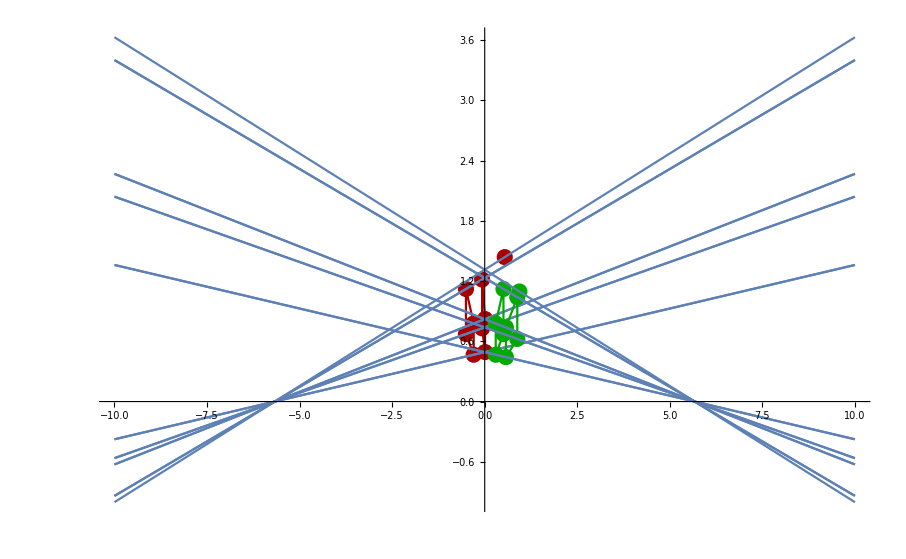

Begin Computing essential Matrix___________________________________________________

EMtx = (-1.53203×10^-15 | -0.122788 | -5.68777×10^-16
-0.122788 | 2.25388×10^-16 | -0.696364
4.0662×10^-16 | 0.696364 | 2.4795×10^-16)

U of E = {{-0.173648,0.,0.984808},{-6.0084×10^-15,-1.,-1.06266×10^-15},{0.984808,-6.32827×10^-15,0.173648}}

Sigma of E = {{0.707107,0.,0.},{0.,0.707107,0.},{0.,0.,0.}}

V of E = {{2.33147×10^-15,0.173648,-0.984808},{1.,-6.66411×10^-15,9.23002×10^-16},{6.41676×10^-15,0.984808,0.173648}}

S1 = (0. | -0.173648 | -1.09889×10^-15
0.173648 | 0. | -0.984808
1.09889×10^-15 | 0.984808 | 0.)

S2 = (0. | 0.173648 | 1.09889×10^-15
-0.173648 | 0. | 0.984808
-1.09889×10^-15 | -0.984808 | 0.)

R1 = (1. | -2.06619×10^-15 | -7.21645×10^-16
-2.33464×10^-15 | -1. | -3.15112×10^-16
-6.66134×10^-16 | 7.43163×10^-17 | -1.)

R2 = (0.939693 | 2.48231×10^-16 | -0.34202
2.41605×10^-16 | 1. | 6.8417×10^-16
0.34202 | -3.94871×10^-16 | 0.939693)

Test R1 is rotation ={{1.,2.68448×10^-16,-5.55112×10^-17},{2.68448×10^-16,1.,2.40796×10^-16},{-5.55112×10^-17,2.40796×10^-16,1.}}

Test R2 is rotation ={{1.,3.39811×10^-16,-1.11022×10^-16},{3.39811×10^-16,1.,2.28212×10^-16},{-1.11022×10^-16,2.28212×10^-16,1.}}

Check if t of S1, S2 is equal = {{{0.984808,-1.11022×10^-15,0.173648}},{{0.984808,-1.11022×10^-15,0.173648}}}

t = {0.984808,-1.11022×10^-15,0.173648}

P21  = (0.939693 | 2.48231×10^-16 | -0.34202 | -0.984808
2.41605×10^-16 | 1. | 6.8417×10^-16 | 1.11022×10^-15
0.34202 | -3.94871×10^-16 | 0.939693 | -0.173648)

P22  = (1. | -2.06619×10^-15 | -7.21645×10^-16 | -0.984808
-2.33464×10^-15 | -1. | -3.15112×10^-16 | 1.11022×10^-15
-6.66134×10^-16 | 7.43163×10^-17 | -1. | -0.173648)

P23  = (0.939693 | 2.48231×10^-16 | -0.34202 | 0.984808
2.41605×10^-16 | 1. | 6.8417×10^-16 | -1.11022×10^-15
0.34202 | -3.94871×10^-16 | 0.939693 | 0.173648)

P24  = (1. | -2.06619×10^-15 | -7.21645×10^-16 | 0.984808
-2.33464×10^-15 | -1. | -3.15112×10^-16 | -1.11022×10^-15
-6.66134×10^-16 | 7.43163×10^-17 | -1. | 0.173648)

End Computing essential Matrix___________________________________________________

PList = {{{0.939693,2.48231×10^-16,-0.34202,-0.984808},{2.41605×10^-16,1.,6.8417×10^-16,1.11022×10^-15},{0.34202,-3.94871×10^-16,0.939693,-0.173648}},{{1.,-2.06619×10^-15,-7.21645×10^-16,-0.984808},{-2.33464×10^-15,-1.,-3.15112×10^-16,1.11022×10^-15},{-6.66134×10^-16,7.43163×10^-17,-1.,-0.173648}},{{0.939693,2.48231×10^-16,-0.34202,0.984808},{2.41605×10^-16,1.,6.8417×10^-16,-1.11022×10^-15},{0.34202,-3.94871×10^-16,0.939693,0.173648}},{{1.,-2.06619×10^-15,-7.21645×10^-16,0.984808},{-2.33464×10^-15,-1.,-3.15112×10^-16,-1.11022×10^-15},{-6.66134×10^-16,7.43163×10^-17,-1.,0.173648}}}

Length PList = 4

End Reconstruction of Rotation and Translation________________________________________________

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{0.376638,0.5,-0.743363},{0.704908,0.5,-0.801245},{0.704908,0.833333,-0.801245},{0.376638,0.833333,-0.743363},{0.318756,0.5,-1.07163},{0.647025,0.5,-1.12951},{0.647025,0.833333,-1.12951},{0.318756,0.833333,-1.07163},{1.13943,1.33333,-1.21634}}

ScaleValue = 7.9652

RForOk2 = {{0.939693,2.41605×10^-16,0.34202},{2.48231×10^-16,1.,-3.94871×10^-16},{-0.34202,6.8417×10^-16,0.939693}}

tForOK2 = {-0.984808,1.11022×10^-15,-0.173648}

t = {0.984808,-9.34332×10^-16,-0.173648}

Reconstructed scaled Points 3D = (3. | 3.9826 | -5.92103
5.61473 | 3.9826 | -6.38208
5.61473 | 6.63767 | -6.38208
3. | 6.63767 | -5.92103
2.53895 | 3.9826 | -8.53576
5.15368 | 3.9826 | -8.99681
5.15368 | 6.63767 | -8.99681
2.53895 | 6.63767 | -8.53576
9.07578 | 10.6203 | -9.68838)

-Graphics3D-

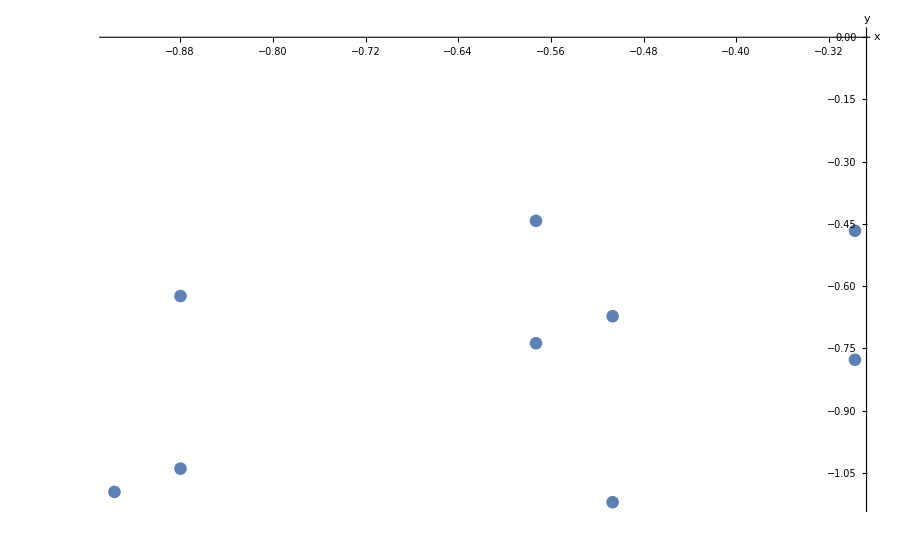

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-1.56348×10^15,-2.07557×10^15,3.0858×10^15},{1.05736,0.75,-1.20187},{1.05736,1.25,-1.20187},{-2.66368×10^14,-5.89355×10^14,5.25725×10^14},{9.86136×10^14,1.54685×10^15,-3.31531×10^15},{0.970537,0.75,-1.69427},{0.970537,1.25,-1.69427},{-5.70975×10^14,-1.49272×10^15,1.91957×10^15},{0.683657,0.8,-0.729803}}

ScaleValue = -1.9188×10^-15

RForOk2 = {{1.,-2.33464×10^-15,-6.66134×10^-16},{-2.06619×10^-15,-1.,7.43163×10^-17},{-7.21645×10^-16,-3.15112×10^-16,-1.}}

tForOK2 = {-0.984808,1.11022×10^-15,-0.173648}

t = {0.984808,-9.11671×10^-16,-0.173648}

Reconstructed scaled Points 3D = (3. | 3.9826 | -5.92103
-2.02887×10^-15 | -1.4391×10^-15 | 2.30614×10^-15
-2.02887×10^-15 | -2.3985×10^-15 | 2.30614×10^-15
0.511108 | 1.13085 | -1.00876
-1.8922 | -2.9681 | 6.36142
-1.86227×10^-15 | -1.4391×10^-15 | 3.25097×10^-15
-1.86227×10^-15 | -2.3985×10^-15 | 3.25097×10^-15
1.09559 | 2.86423 | -3.68328
-1.3118×10^-15 | -1.53504×10^-15 | 1.40035×10^-15)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-0.376638,-0.5,0.743363},{-0.704908,-0.5,0.801245},{-0.704908,-0.833333,0.801245},{-0.376638,-0.833333,0.743363},{-0.318756,-0.5,1.07163},{-0.647025,-0.5,1.12951},{-0.647025,-0.833333,1.12951},{-0.318756,-0.833333,1.07163},{-1.13943,-1.33333,1.21634}}

ScaleValue = -7.9652

RForOk2 = {{0.939693,2.41605×10^-16,0.34202},{2.48231×10^-16,1.,-3.94871×10^-16},{-0.34202,6.8417×10^-16,0.939693}}

tForOK2 = {0.984808,-1.11022×10^-15,0.173648}

t = {-0.984808,9.34332×10^-16,0.173648}

Reconstructed scaled Points 3D = (3. | 3.9826 | -5.92103
5.61473 | 3.9826 | -6.38208
5.61473 | 6.63767 | -6.38208
3. | 6.63767 | -5.92103
2.53895 | 3.9826 | -8.53576
5.15368 | 3.9826 | -8.99681
5.15368 | 6.63767 | -8.99681
2.53895 | 6.63767 | -8.53576
9.07578 | 10.6203 | -9.68838)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{1.56348×10^15,2.07557×10^15,-3.0858×10^15},{-1.05736,-0.75,1.20187},{-1.05736,-1.25,1.20187},{2.66368×10^14,5.89355×10^14,-5.25725×10^14},{-9.86136×10^14,-1.54685×10^15,3.31531×10^15},{-0.970537,-0.75,1.69427},{-0.970537,-1.25,1.69427},{5.70975×10^14,1.49272×10^15,-1.91957×10^15},{-0.683657,-0.8,0.729803}}

ScaleValue = 1.9188×10^-15

RForOk2 = {{1.,-2.33464×10^-15,-6.66134×10^-16},{-2.06619×10^-15,-1.,7.43163×10^-17},{-7.21645×10^-16,-3.15112×10^-16,-1.}}

tForOK2 = {0.984808,-1.11022×10^-15,0.173648}

t = {-0.984808,9.11671×10^-16,0.173648}

Reconstructed scaled Points 3D = (3. | 3.9826 | -5.92103
-2.02887×10^-15 | -1.4391×10^-15 | 2.30614×10^-15
-2.02887×10^-15 | -2.3985×10^-15 | 2.30614×10^-15
0.511108 | 1.13085 | -1.00876
-1.8922 | -2.9681 | 6.36142
-1.86227×10^-15 | -1.4391×10^-15 | 3.25097×10^-15
-1.86227×10^-15 | -2.3985×10^-15 | 3.25097×10^-15
1.09559 | 2.86423 | -3.68328
-1.3118×10^-15 | -1.53504×10^-15 | 1.40035×10^-15)

-Graphics3D-

-Graphics-

Begin New Rectification with Disortion minimization criterion_______________________________________________

pi = {{0.506669,0.672619,1.},{0.879765,0.624029,1.},{0.879765,1.04005,1.},{0.506669,1.12103,1.},{0.297449,0.466578,1.},{0.572835,0.442668,1.},{0.572835,0.73778,1.},{0.297449,0.77763,1.},{0.936769,1.09619,1.}}

pj = {{-0.506669,0.672619,1.},{-0.0705625,0.729416,1.},{-0.0705625,1.21569,1.},{-0.506669,1.12103,1.},{-0.297449,0.466578,1.},{0.00938452,0.493219,1.},{0.00938452,0.822031,1.},{-0.297449,0.77763,1.},{0.541487,1.43845,1.}}

n = 9

minXpi = 0.297449

maxXPi = 0.936769

minYpi = 0.442668

maxYPi = 1.12103

minXPj = -0.506669

maxXPj = 0.541487

minYPj = 0.466578

maxYPj = 1.43845

piWidth = 3.

piHeight = 3.

pjWidth = 3.

pjHeight = 3.

pc = (0.605578
0.775397
1.)

pcPrime = (-0.132123
0.85963
1.)

P = {{-0.0989096,0.274187,0.274187,-0.0989096,-0.308129,-0.0327436,-0.0327436,-0.308129,0.331191},{-0.102777,-0.151368,0.264651,0.345635,-0.308819,-0.332729,-0.0376166,0.00223357,0.320789},{0.,0.,0.,0.,0.,0.,0.,0.,0.}}

PPrime = {{-0.374546,0.0615602,0.0615602,-0.374546,-0.165326,0.141507,0.141507,-0.165326,0.673609},{-0.18701,-0.130214,0.356064,0.261402,-0.393052,-0.366411,-0.0375985,-0.0819994,0.578818},{0.,0.,0.,0.,0.,0.,0.,0.,0.}}

PP = {{0.471642,0.219877,0.},{0.219877,0.533382,0.},{0.,0.,0.}}

PPPrime = {{0.836612,0.397306,0.},{0.397306,0.878956,0.},{0.,0.,0.}}

pc = {0.605578,0.775397,1.}

pcpc = {{0.366725,0.469563,0.605578},{0.469563,0.60124,0.775397},{0.605578,0.775397,1.}}

pcpcPrime = {{0.0174564,-0.113577,-0.132123},{-0.113577,0.738963,0.85963},{-0.132123,0.85963,1.}}

A = (0.0160834 | -0.00663009 | -0.0912138
-0.00663009 | 0.0142218 | 0.0376011
-0.0912138 | 0.0376011 | 0.517299)

B = (0.0090648 | 0.0733799 | -0.051409
0.0733799 | 0.594012 | -0.416158
-0.051409 | -0.416158 | 0.291555)

APrime = (0.0265038 | -0.0119802 | 0.15031
-0.0119802 | 0.0252269 | -0.0679432
0.15031 | -0.0679432 | 0.852452)

BPrime = (-2.13654×10^-17 | -0.011034 | 3.21598×10^-17
0.0111412 | -1.31778×10^-16 | -0.35834
-6.00356×10^-17 | -0.473626 | 1.48426×10^-16)

{A[[1,1;;2]],A[[2,1;;2]]}={{0.0160834,-0.00663009},{-0.00663009,0.0142218}}

{APrime[[1,1;;2]],APrime[[2,1;;2]]}={{0.0265038,-0.0119802},{-0.0119802,0.0252269}}

DD ={{0.126821,-0.0522793},{0.,0.107185}}

DDPrime ={{0.1628,-0.0735887},{0.,0.140754}}

{B[[1,1;;2]],B[[2,1;;2]]}={{0.0090648,0.0733799},{0.0733799,0.594012}}

{BPrime[[1,1;;2]],BPrime[[2,1;;2]]}={{-2.13654×10^-17,-0.011034},{0.0111412,-1.31778×10^-16}}

DTBD[[2,1]] = {0.0988603,0.995101}

Eigensystem DTB1 = {{57.668,0.},{{0.0988603,0.995101},{-0.995101,0.0988603}}}

Eigensystem DTBPrimeD = {{0.00122367+0.483857 ⅈ,0.00122367-0.483857 ⅈ},{{-0.00178393+0.705392 ⅈ,0.708815+0. ⅈ},{-0.00178393-0.705392 ⅈ,0.708815+0. ⅈ}}}

z1 first = {4.60666,9.28396}

z1= {4.60666,9.28396}

z2 first = {2.26535+4.33288 ⅈ,5.03585+0. ⅈ}

GreaterEqual::nord: Invalid comparison with 0.00122367-0.483857 ⅈ attempted.

z2= {2.26535+4.33288 ⅈ,5.03585+0. ⅈ}

z ={17.383+0. ⅈ,17.383+0. ⅈ,0.}

w = {3.01852+0. ⅈ,-3.01852+0. ⅈ,-17.1189+0. ⅈ}

wPrime = {-2.13442+0. ⅈ,-2.13442+0. ⅈ,-12.1049+0. ⅈ}

wPrime = {0.176327+0. ⅈ,0.176327+0. ⅈ,1.+0. ⅈ}

w = {-0.176327+0. ⅈ,0.176327+0. ⅈ,1.+0. ⅈ}

HpPrime = (1. | 0. | 0.
0. | 1. | 0.
0.176327+0. ⅈ | 0.176327+0. ⅈ | 1.+0. ⅈ)

Hp = (1. | 0. | 0.
0. | 1. | 0.
-0.176327+0. ⅈ | 0.176327+0. ⅈ | 1.+0. ⅈ)

ePrime inf = {-0.984808+0. ⅈ,1.14505×10^-15+0. ⅈ,-1.85962×10^-15+0. ⅈ}

e inf = {-0.984808+0. ⅈ,9.23002×10^-16+0. ⅈ,0.+0. ⅈ}

HrPrime = (-0.696364+0. ⅈ | 5.25057×10^-16+0. ⅈ | 0.
-5.25057×10^-16+0. ⅈ | -0.696364+0. ⅈ | 0.705
0. | 0. | 1.)

Hr = (-0.696364+0. ⅈ | 3.629×10^-16+0. ⅈ | 0.
-3.629×10^-16+0. ⅈ | -0.696364+0. ⅈ | 0.705
0. | 0. | 1.)

ePrimeHorizontal = {0.685785+0. ⅈ,-1.59132×10^-15+0. ⅈ,-1.85962×10^-15+0. ⅈ}

eHorizontal = {0.685785+0. ⅈ,-2.85359×10^-16+0. ⅈ,0.+0. ⅈ}

piA = {-1.04455+0. ⅈ,0.518534+0. ⅈ,0.73551+0. ⅈ}

piB = {-2.08909+0. ⅈ,-0.526012+0. ⅈ,0.73551+0. ⅈ}

piC = {-1.04455+0. ⅈ,-1.19763+0. ⅈ,1.26449+0. ⅈ}

piD = {5.4435×10^-16+0. ⅈ,-0.153081+0. ⅈ,1.26449+0. ⅈ}

piX = {-2.08909+0. ⅈ,-0.372932+0. ⅈ,-0.528981+0. ⅈ}

piY = {1.11022×10^-15+0. ⅈ,-1.71616+0. ⅈ,0.528981+0. ⅈ}

piSA = -0.860278+0. ⅈ

piSB = 0.217306+0. ⅈ

pjA = {-1.04455+0. ⅈ,0.891466+0. ⅈ,1.26449+0. ⅈ}

pjB = {-2.08909+0. ⅈ,0.219851+0. ⅈ,1.79347+0. ⅈ}

pjC = {-1.04455+0. ⅈ,-0.824695+0. ⅈ,1.79347+0. ⅈ}

pjD = {7.87585×10^-16+0. ⅈ,-0.153081+0. ⅈ,1.26449+0. ⅈ}

pjX = {-2.08909+0. ⅈ,0.372932+0. ⅈ,0.528981+0. ⅈ}

pjY = {1.55431×10^-15+0. ⅈ,-1.71616+0. ⅈ,0.528981+0. ⅈ}

pjSA = -0.860278+0. ⅈ

pjSB = -0.217306+0. ⅈ

RecPointsC1 =(0.492264+0. ⅈ | 0.653497+0. ⅈ | 1.+0. ⅈ
0.92131+0. ⅈ | 0.653497+0. ⅈ | 1.+0. ⅈ
0.855584+0. ⅈ | 1.01146+0. ⅈ | 1.+0. ⅈ
0.457146+0. ⅈ | 1.01146+0. ⅈ | 1.+0. ⅈ
0.288835+0. ⅈ | 0.453067+0. ⅈ | 1.+0. ⅈ
0.586291+0. ⅈ | 0.453067+0. ⅈ | 1.+0. ⅈ
0.556645+0. ⅈ | 0.716929+0. ⅈ | 1.+0. ⅈ
0.27423+0. ⅈ | 0.716929+0. ⅈ | 1.+0. ⅈ)

RecPointsC2 =(-0.492264+0. ⅈ | 0.653497+0. ⅈ | 1.+0. ⅈ
-0.0632182+0. ⅈ | 0.653497+0. ⅈ | 1.+0. ⅈ
-0.0587083+0. ⅈ | 1.01146+0. ⅈ | 1.+0. ⅈ
-0.457146+0. ⅈ | 1.01146+0. ⅈ | 1.+0. ⅈ
-0.288835+0. ⅈ | 0.453067+0. ⅈ | 1.+0. ⅈ
0.00862055+0. ⅈ | 0.453067+0. ⅈ | 1.+0. ⅈ
0.00818465+0. ⅈ | 0.716929+0. ⅈ | 1.+0. ⅈ
-0.27423+0. ⅈ | 0.716929+0. ⅈ | 1.+0. ⅈ)

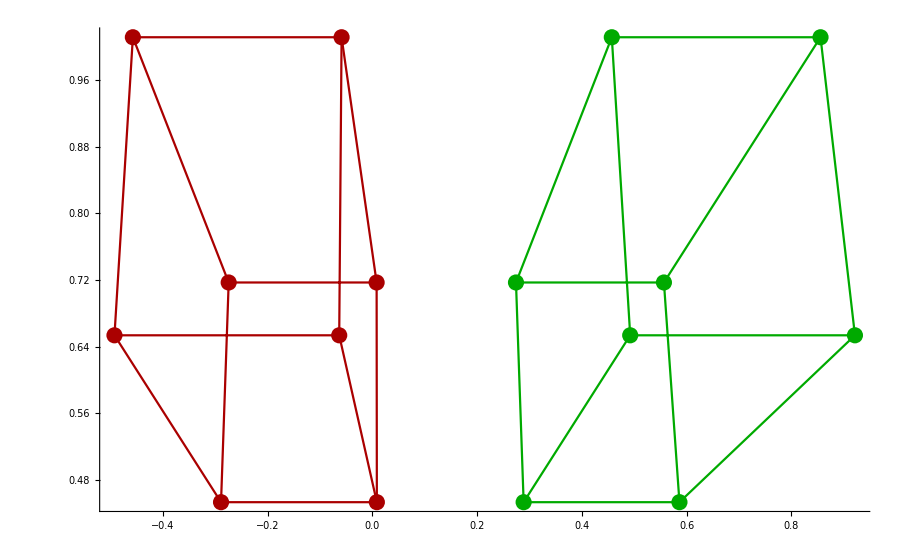

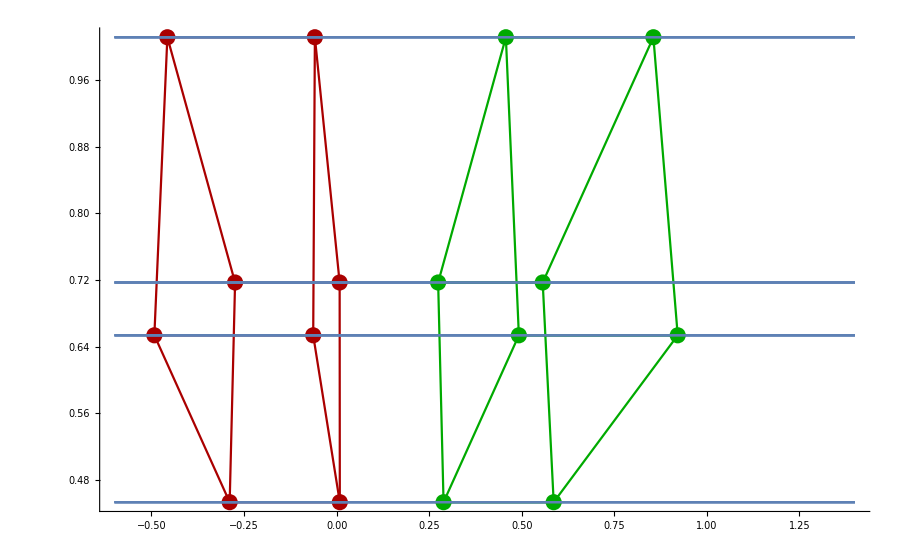

End New Rectification with Disortion minimization criterion_______________________________________________

```mathematica
StartComputation[];
```